```mathematica
Needs["Quantum`Notation`"]
SetComputingAliases[];
```

```mathematica
(*4-qubit half-braiding*)


(*State Preparation Circuit*)
```

```mathematica
QuantumPlot3D[QubitMeasurement[(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[2]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩,{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}]]
```

-Graphics3D-

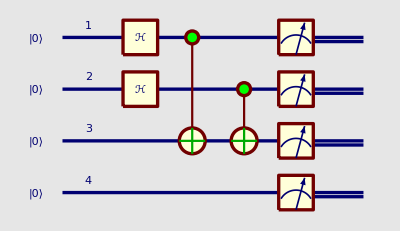

```mathematica
QuantumPlot[QubitMeasurement[(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[2]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩,{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}]]
```

```mathematica
QuantumEvaluate[QubitMeasurement[(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[2]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩,{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}]]
```

Probability | Measurement | State
1/4 | {{0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗|0_OverHat[4]⟩
1/4 | {{0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗|0_OverHat[4]⟩
1/4 | {{1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗|0_OverHat[4]⟩
1/4 | {{1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗|0_OverHat[4]⟩
Probability | Measurement | State

```mathematica
(* half-braiding *)
```

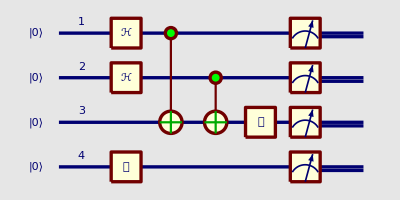

```mathematica
QuantumPlot[QubitMeasurement[Subscript[𝒳, OverHat[4]]·Subscript[𝒳, OverHat[3]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[2]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩,{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}]]
```

```mathematica
QuantumEvaluate[QubitMeasurement[Subscript[𝒳, OverHat[4]]·Subscript[𝒳, OverHat[3]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[ℋ, OverHat[2]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩,{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}]]
```

Probability | Measurement | State
1/4 | {{0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗|1_OverHat[4]⟩
1/4 | {{0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗|1_OverHat[4]⟩
1/4 | {{1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗|1_OverHat[4]⟩
1/4 | {{1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗|1_OverHat[4]⟩
Probability | Measurement | State

```mathematica
Hami =
```